```mathematica
Clear["Global`*"]
```

# Thermodynamic potentials visualization

The energies of ideal gas

## Mathematical definition of potentials

𝒰=𝒰(S,V), ℋ=ℋ(S,P), ℱ=ℱ(T,V), 𝒢=𝒢(T,P),
where S is an entropy, P - pressure, V - volume, T - temperature, 𝒰 - internal energy, ℋ - enthalpy, ℱ - free energy of Helmholtz, 𝒢 - free energy of Gibbs.

Definition and visualize the function of free energy of Gibbs of the system of ideal gas, function was chosen randomly, so it may be fully non-physical results:

```mathematica
helmholtzFreeEnergy[temperature_,volume_]:=Log[temperature]^2 volume;
```

Plotting the Helmholtz free energy

```mathematica
Plot3D[
helmholtzFreeEnergy[x,y],{x,1,273},{y,1,100},
ViewPoint->{1.3,-2.4,2.},
TicksStyle->Directive[FontFamily->"Times New Roman",14],
AxesLabel->(Style[#1,FontFamily->"Times",14,Bold]&)/@{"𝒯","𝒫","ℱ"}
]
```

-Graphics3D-

Next we will try to visualise the others potential with using the definition of Free Helmholtz energy by using the Helmholtz-Gibbs equations.

Definition of the thermodynamic potentials

```mathematica
internalEnergy[temperature_,volume_]:=-temperature^2 Derivative[1,0][Function[{x,y},helmholtzFreeEnergy[x,y]/x]][temperature,volume]
enthalpy[temperature_,volume_]:=-temperature^2 Derivative[1,0][Function[{x,y},helmholtzFreeEnergy[x,y]/x]][temperature,volume]-volume*Derivative[1,0][Function[{x,y},helmholtzFreeEnergy[x,y]]][temperature,volume]
gibbsFreeEnergy[temperature_,volume_]:=helmholtzFreeEnergy[temperature,volume]-volume*Derivative[1,0][Function[{x,y},helmholtzFreeEnergy[x,y]]][temperature,volume]
```

Plotting the Internal Energy of the system

```mathematica
Plot3D[
internalEnergy[x,y],{x,1,273},{y,1,100},
ViewPoint->{1.3,-2.4,2.},
TicksStyle->Directive[FontFamily->"Times New Roman",14],
AxesLabel->(Style[#1,FontFamily->"Times",14,Bold]&)/@{"𝒯","𝒫","𝒰"}
]
```

-Graphics3D-

Plotting the Enthalpy of the system

```mathematica
Plot3D[
enthalpy[x,y],{x,1,273},{y,1,100},
ViewPoint->{1.3,-2.4,2.},
TicksStyle->Directive[FontFamily->"Times New Roman",14],
AxesLabel->(Style[#1,FontFamily->"Times",14,Bold]&)/@{"𝒯","𝒫","ℋ"}
]
```

-Graphics3D-

Plotting the Gibbs Free Energy of the system

```mathematica
Plot3D[
gibbsFreeEnergy[x,y],{x,1,273},{y,1,100},
ViewPoint->{1.3,-2.4,2.},
TicksStyle->Directive[FontFamily->"Times New Roman",14],
AxesLabel->(Style[#1,FontFamily->"Times",14,Bold]&)/@{"𝒯","𝒫","𝒢"}
]
```

-Graphics3D-

Now, we can build a histogram to visualise the potentials in any point of Temperature-Volume region.

Defining the random point in region

```mathematica
randomPoint={RandomReal[{1,273}],RandomReal[{1,100}]};
```

Building of the barchart of the potentials values

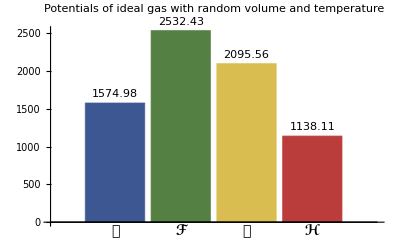

```mathematica
BarChart[
{internalEnergy@@randomPoint,helmholtzFreeEnergy@@randomPoint,gibbsFreeEnergy@@randomPoint,enthalpy@@randomPoint},
ChartStyle->"DarkRainbow",
ChartLabels->(Style[#1,FontFamily->"Times",14,Bold]&)/@{"𝒰","ℱ","𝒢","ℋ"},
PlotLabel->(Style[#1,FontFamily->"Times",14,Bold]&)@"Potentials of ideal gas with random volume and temperature",
TicksStyle->Directive[FontFamily->"Times New Roman",14],
LabelingFunction->(Placed[#,Above]&)
]
```

Also we can extract entropy and pressure from initial function of Helmholtz Free energy by the equations of state.

Defining the functions of Pressure and Entropy

## Add more sections as needed to explain the topic (cmd/alt+4)

Section names, the total number of sections, and section organization will differ based on the topic.

Here are some ideas for sections you might consider:

history/origins
derivation
applications
common misunderstandings
recent developments
unanswered questions

Further Explorations

Name of a related topic for exploration

Name of another related topics for exploration (repeat as needed)

Authorship information

Name of Author

Date of creation

Author email address (please use the email associated with your Wolfram User ID)